# MATH 6250 - Surfaces

## Alexander Winkles

## Functions

```mathematica
norm[j_] := FullSimplify[√TrigReduce[j[[1]]^2+j[[2]]^2+j[[3]]^2]]  (* Created new norm function with less bugs *)
```

```mathematica
Surface[x_,u_,v_] := Module[{xu,xv,nvec,Ip,IIp,E,F,G,area,l,m,n,Sp,K,H,k1,k2, Vec,uvec1,uvec2,ugraph,vgraph,vvec1,vvec2, uuu,uuv,vvv,vvu,uvu,uvv,christ1,christ2,christ3(*geo,geosolve*)},

(* Computes initial terms to develop the First Fundamental Form *)
xu = D[x[u,v],u];
xv = D[x[u,v],v];
nvec = Cross[xu,xv]/norm[Cross[xu,xv]];
E = FullSimplify[Dot[xu,xu]];
F = FullSimplify[Dot[xu,xv]];
G = FullSimplify[Dot[xv,xv]];
Ip =({{E, F}, {F, G}});

(* Computes terms to develop the Second Fundamental Form *)
l = FullSimplify[Dot[D[xu,u],nvec]];
m = FullSimplify[Dot[D[xu,v],nvec]];
n = FullSimplify[Dot[D[xv,v],nvec]];
IIp = ({{l, m}, {m, n}});

(* Computes the Shape Operator, Gaussian curvature, and mean curvature *)
Sp = FullSimplify[Inverse[Ip].IIp];
K = FullSimplify[Det[Sp]];
H = FullSimplify[Tr[Sp]/2];

(* Computes the principal directions and the principal curvatures and creates a mesh of the surface *)
k1 =FullSimplify[ H + Sqrt[H^2-K]];
k2 = FullSimplify[H - Sqrt[H^2-K]];
Vec = Eigenvectors[Sp];
uvec1 = ReplaceAll[Vec[[1,1]],u-> u[v]];
uvec2 = ReplaceAll[Vec[[1,2]],u-> u[v]];
vvec1 = ReplaceAll[Vec[[2,1]],v-> v[u]];
vvec2 = ReplaceAll[Vec[[2,2]],v-> v[u]];
ugraph = Show[Table[Module[{usol},
usol = DSolve[{u'[v]==uvec1/uvec2,u[0]==i},u[v],v];ParametricPlot3D[x[(u[v]/.usol),v],{v,-4,4}]],{i,-10,10,1.0}],PlotRange-> {{-4,4},{-4,4},{-4,4}}];
vgraph = Show[Table[Module[{vsol},
vsol = DSolve[{v'[u]==vvec2/vvec1,v[0]==j},v[u],u];ParametricPlot3D[x[u,(v[u]/.vsol)],{u,-4,4}]],{j,-10,10,1.0}],PlotRange-> {{-4,4},{-4,4},{-4,4}}];

(* Computes the Christoffel symbols *)
christ1 = Inverse[{{E,F},{F,G}}].{1/2 D[E,u],D[F,u]-1/2 D[E,v]};
christ2 = Inverse[{{E,F},{F,G}}].{1/2 D[E,v],1/2 D[G,u]};
christ3 = Inverse[{{E,F},{F,G}}].{D[F,v]-1/2 D[G,u],1/2 D[G,v]};
uuu =  FullSimplify[christ1[[1]]];
uuv =FullSimplify[christ1[[2]]];
uvu =FullSimplify[christ2[[1]]];
uvv = FullSimplify[christ2[[2]]];
vvu =FullSimplify[christ3[[1]]];
vvv =FullSimplify[christ3[[2]]];

(* Geodesic equations *)

(*geo[p_,q_]:={p,q,-(uuu (p)^2 + 2uvu p q+ vvu (q)^2 ),-( uuv (p)^2 + 2uvv p q + vvv (q)^2 )};
geosolve = NDSolve[u''[t]==First[Take[geo[
geo1 = NDSolve[{u''[t] ==-( uuu (u'[t])^2 + 2uvu u'[t]v'[t] + vvu (v'[t])^2 ),v''[t] ==-( uuv (u'[t])^2 + 2uvv u'[t]v'[t] + vvv (v'[t])^2 ),u[0]==0,v[0]==0,u'[0]==1,v'[0]==1},{u[t],v[t]},{t,0,8}];*)

(* Returns Surface results *)
CellPrint[{
Cell[TextData[{"Ip = ",Cell[BoxData[ToBoxes[MatrixForm[Ip]]]]}],"Text"],
Cell[TextData[{"IIp = ",Cell[BoxData[ToBoxes[MatrixForm[IIp]]]]}],"Text"],
Cell[TextData[{"Sp = ",Cell[BoxData[ToBoxes[MatrixForm[Sp]]]]}],"Text"],
Cell[TextData[{"k1 = ", Cell[BoxData[ToBoxes[k1]]]}],"Text"],
Cell[TextData[{"k2 = ", Cell[BoxData[ToBoxes[k2]]]}],"Text"],
Cell[TextData[{"K = ",Cell[BoxData[ToBoxes[K]]]}],"Text"],
Cell[TextData[{"H = ",Cell[BoxData[ToBoxes[H]]]}],"Text"],
Cell[TextData[{"Vec = ",Cell[BoxData[ToBoxes[MatrixForm[Vec]]]]}],"Text"],
Cell[BoxData[ToBoxes[Show[ugraph,vgraph]]],"Output"],
Cell[TextData[{"uuu = ",Cell[BoxData[ToBoxes[uuu]]]}],"Text"] ,
Cell[TextData[{"uuv = ",Cell[BoxData[ToBoxes[uuv]]]}],"Text"] ,
Cell[TextData[{"uvu = ",Cell[BoxData[ToBoxes[uvu]]]}],"Text"] ,
Cell[TextData[{"uvv = ",Cell[BoxData[ToBoxes[uvv]]]}],"Text"] ,
Cell[TextData[{"vvu = ",Cell[BoxData[ToBoxes[vvu]]]}],"Text"] ,
Cell[TextData[{"vvv = ",Cell[BoxData[ToBoxes[vvv]]]}],"Text"] 
}]
(*{geo[p,q]}*)
];
```

## Test

```mathematica
x[u_,v_]:={Sin[u]Cos[v],Sin[u]Sin[v],Cos[u]};
```

```mathematica
Surface[x,u,v]
```

Ip = (1 | 0
0 | Sin[u]^2)

IIp = (-Csc[u] √(Sin[u]^2) | 0
0 | -Sin[u] √(Sin[u]^2))

Sp = (-Csc[u] √(Sin[u]^2) | 0
0 | -Csc[u] √(Sin[u]^2))

k1 = -Csc[u] √(Sin[u]^2)

k2 = -Csc[u] √(Sin[u]^2)

K = 1

H = -Csc[u] √(Sin[u]^2)

Vec = (0 | 1
1 | 0)

-Graphics3D-

uuu = 0

uuv = 0

uvu = 0

uvv = Cot[u]

vvu = -Cos[u] Sin[u]

vvv = 0

```mathematica
x[u_,v_] := {u,v,u v};
```

```mathematica
Surface[x,u,v]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve :: ifun will be suppressed during this calculation.

Ip = (1+v^2 | u v
u v | 1+u^2)

IIp = (0 | 1/(√(1+u^2+v^2))
1/(√(1+u^2+v^2)) | 0)

Sp = (-(u v)/((1+u^2+v^2)^(3/2)) | (1+u^2)/((1+u^2+v^2)^(3/2))
(1+v^2)/((1+u^2+v^2)^(3/2)) | -(u v)/((1+u^2+v^2)^(3/2)))

k1 = √(((1+u^2) (1+v^2))/((1+u^2+v^2)^3))-(u v)/((1+u^2+v^2)^(3/2))

k2 = -√(((1+u^2) (1+v^2))/((1+u^2+v^2)^3))-(u v)/((1+u^2+v^2)^(3/2))

K = -1/((1+u^2+v^2)^2)

H = -(u v)/((1+u^2+v^2)^(3/2))

Vec = (-(√((1+u^2) (1+v^2)))/(1+v^2) | 1
(√((1+u^2) (1+v^2)))/(1+v^2) | 1)

-Graphics3D-

uuu = 0

uuv = 0

uvu = v/(1+u^2+v^2)

uvv = u/(1+u^2+v^2)

vvu = 0

vvv = 0

```mathematica
Export["/home/alexander/Desktop/surface.stl",-Graphics3D-,"STL"]
```

Export::nodta: STL contains no data that can be exported to the STL format.

$Failed

```mathematica
x[u_,v_]:={(3+Cos[u])Cos[v],(3+Cos[u])Sin[v],Sin[u]};
```

```mathematica
Surface[x,u,v]
```

Ip = (1 | 0
0 | (3+Cos[u])^2)

IIp = ((3+Cos[u])/(√((3+Cos[u])^2)) | 0
0 | Cos[u] √((3+Cos[u])^2))

Sp = ((3+Cos[u])/(√((3+Cos[u])^2)) | 0
0 | Cos[u]/(√((3+Cos[u])^2)))

k1 = (3+2 Cos[u]+3 √(1/(3+Cos[u])^2) √((3+Cos[u])^2))/(2 √((3+Cos[u])^2))

k2 = (3+2 Cos[u]-3 √(1/(3+Cos[u])^2) √((3+Cos[u])^2))/(2 √((3+Cos[u])^2))

K = 1/(1+3 Sec[u])

H = (3+2 Cos[u])/(2 √((3+Cos[u])^2))

Vec = (0 | 1
1 | 0)

-Graphics3D-

uuu = 0

uuv = 0

uvu = 0

uvv = -Sin[u]/(3+Cos[u])

vvu = (3+Cos[u]) Sin[u]

vvv = 0

```mathematica
x[u_,v_]:={u Cos[v],u Sin[v],v};
```

```mathematica
Surface[x,u,v]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve :: ifun will be suppressed during this calculation.

Ip = (1 | 0
0 | 1+u^2)

IIp = (0 | -1/(√(1+u^2))
-1/(√(1+u^2)) | 0)

Sp = (0 | -1/(√(1+u^2))
-1/((1+u^2)^(3/2)) | 0)

k1 = √(1/((1+u^2)^2))

k2 = -√(1/((1+u^2)^2))

K = -1/((1+u^2)^2)

H = 0

Vec = (√(1+u^2) | 1
-√(1+u^2) | 1)

-Graphics3D-

uuu = 0

uuv = 0

uvu = 0

uvv = u/(1+u^2)

vvu = -u

vvv = 0

```mathematica
x[u_,v_] := 4{Cosh[u]Cos[v],Cosh[u]Sin[v],u};
```

```mathematica
Surface[x,u,v]
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Ip = (16 Cosh[u]^2 | 0
0 | 16 Cosh[u]^2)

IIp = (-4 √(Cosh[u]^4) Sech[u]^2 | 0
0 | 4 √(Cosh[u]^4) Sech[u]^2)

Sp = (-1/(4 √(Cosh[u]^4)) | 0
0 | 1/(4 √(Cosh[u]^4)))

K = -1/16 Sech[u]^4

H = 0

Vec = (1 | 0
0 | 1)

-Graphics3D-

```mathematica
x[u_,v_]:=2{Sin[u]Cos[v],Sin[u]Sin[v],Cos[u]};
```

```mathematica
Surface[x,u,v]
```

Ip = (4 | 0
0 | 4 Sin[u]^2)

IIp = (-2 Csc[u] √(Sin[u]^2) | 0
0 | -2 Sin[u] √(Sin[u]^2))

Sp = (-1/2 Csc[u] √(Sin[u]^2) | 0
0 | -1/2 Csc[u] √(Sin[u]^2))

K = 1/4

H = -1/2 Csc[u] √(Sin[u]^2)

Vec = (0 | 1
1 | 0)

-Graphics3D-

## Homework 5

### Problem 3

#### A

```mathematica
q[u_,v_]:= a{Cos[v]Sin[u],Sin[u]Sin[v],Cos[u]};
```

```mathematica
Surface[q,u,v]
```

Ip = (a^2 | 0
0 | a^2 Sin[u]^2)

IIp = (-(a^3 Sin[u])/(√(a^4 Sin[u]^2)) | 0
0 | -(Sin[u] √(a^4 Sin[u]^2))/a)

Sp = (-(a Sin[u])/(√(a^4 Sin[u]^2)) | 0
0 | -(a Sin[u])/(√(a^4 Sin[u]^2)))

K = 1/a^2

H = -(a Sin[u])/(√(a^4 Sin[u]^2))

#### B

```mathematica
q[u_,v_]:={(a+b Cos[u])Cos[v],(a+b Cos[u])Sin[v],b Sin[u]}
```

```mathematica
Surface[q,u,v]
```

Ip = (b^2 | 0
0 | (a+b Cos[u])^2)

IIp = ((√(b^2 (a+b Cos[u])^2))/(a+b Cos[u]) | 0
0 | (Cos[u] √(b^2 (a+b Cos[u])^2))/b)

Sp = ((a+b Cos[u])/(√(b^2 (a+b Cos[u])^2)) | 0
0 | (b Cos[u])/(√(b^2 (a+b Cos[u])^2)))

K = 1/(b^2+a b Sec[u])

H = (a+2 b Cos[u])/(2 √(b^2 (a+b Cos[u])^2))

#### C

```mathematica
q[u_,v_]:= {u Cos[v],u Sin[v],v};
```

```mathematica
Surface[q,u,v]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve :: ifun will be suppressed during this calculation.

Ip = (1 | 0
0 | 1+u^2)

IIp = (0 | -1/(√(1+u^2))
-1/(√(1+u^2)) | 0)

Sp = (0 | -1/(√(1+u^2))
-1/((1+u^2)^(3/2)) | 0)

K = -1/((1+u^2)^2)

H = 0

Vec = (√(1+u^2) | 1
-√(1+u^2) | 1)

-Graphics3D-

#### D

```mathematica
q[u_,v_]:= {Cosh[u]Cos[v],Cosh[u]Sin[v],u}
```

```mathematica
Surface[q,u,v]
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Ip = (Cosh[u]^2 | 0
0 | Cosh[u]^2)

IIp = (-√(Cosh[u]^4) Sech[u]^2 | 0
0 | √(Cosh[u]^4) Sech[u]^2)

Sp = (-1/(√(Cosh[u]^4)) | 0
0 | 1/(√(Cosh[u]^4)))

K = -Sech[u]^4

H = 0

Vec = (1 | 0
0 | 1)

-Graphics3D-

### Problem 8

```mathematica
q[u_,v_]:= {(2u)/(u^2+v^2+1),(2v)/(u^2+v^2+1),(u^2+v^2-1)/(u^2+v^2+1)}
```

```mathematica
Surface[q,u,v]
```

Ip = (4/((1+u^2+v^2)^2) | 0
0 | 4/((1+u^2+v^2)^2))

IIp = (4 √(1/((1+u^2+v^2)^4)) | 0
0 | 4 √(1/((1+u^2+v^2)^4)))

Sp = (√(1/((1+u^2+v^2)^4)) (1+u^2+v^2)^2 | 0
0 | √(1/((1+u^2+v^2)^4)) (1+u^2+v^2)^2)

K = 1

H = √(1/((1+u^2+v^2)^4)) (1+u^2+v^2)^2

Vec = (0 | 1
1 | 0)

-Graphics3D-

### Problem 16

```mathematica
q[u_,v_]:=a {Cosh[u]Cos[v],Cosh[u]Sin[v],u};
```

```mathematica
Surface[q,u,v]
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Ip = (a^2 Cosh[u]^2 | 0
0 | a^2 Cosh[u]^2)

IIp = (-(a^3 Cosh[u]^2)/(√(a^4 Cosh[u]^4)) | 0
0 | (a^3 Cosh[u]^2)/(√(a^4 Cosh[u]^4)))

Sp = (-a/(√(a^4 Cosh[u]^4)) | 0
0 | a/(√(a^4 Cosh[u]^4)))

K = -Sech[u]^4/a^2

H = 0

-Graphics3D-

```mathematica
Integrate[a^2 Cosh[u]^2,{u,-1/a,1/a},{v,0,2 Pi}]
```

a π (2+a Sinh[2/a])

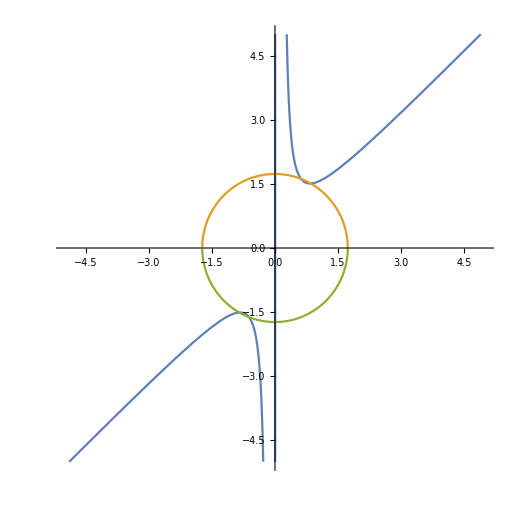

```mathematica
Plot[{{t Cosh[1/t]},{Sqrt[3-t^2]},{-Sqrt[3-t^2]}},{t,-5,5},AspectRatio -> Automatic,PlotRange->{{-5,5},{-5,5}}]
```